# 3 - D Square Well

```mathematica
V[x,y,z]==0 (* for 0<x,y,z<a )
```

```mathematica
(* the schrodinger equation is *)
-ℏ^2/(2m)(D[ψ[x,y,z],{x,2}]+D[ψ[x,y,z],{y,2}]+D[ψ[x,y,z],{z,2}])== Ε ψ[x,y,z]
```

```mathematica
(* seperating varible *)
ψ[x,y,z] == X[x]Y[y]Z[z]
```

```mathematica
-ℏ^2/(2m)(D[ψ[x,y,z],{x,2}]+D[ψ[x,y,z],{y,2}]+D[ψ[x,y,z],{z,2}])== E ψ[x,y,z]
```

```mathematica
(* we have decoupled equation *)
D[X[x],{x,2}]== - (2m Ex)/ℏ^2 X[x]== -kx^2 X[x]
Ex+Ey+Ez== Ε
kx^2+ky^2+kz^2=k^2=(2m Ε)/ℏ^2
```

```mathematica
(* the solution is *)
ψ[x,y,z]==A Sin[kx x]Sin[ky y]Sin[kz z]
(* BC gives *)
kx == nx π/a
(nx^2+ny^2+nz^2)π^2/a^2= k^2 
(nx^2+ny^2+nz^2)(π^2 ℏ^2)/(2m a^2)= Ε
```

```mathematica
(* the nomralization conditon gives *)
Integrate[(Sin[ n π/a x])^2,{x,0,a}]/.n-> 1
```

a/2

```mathematica
(* the solution is *)
ψ[x,y,z]==(2/a)^(1/3)Sin[kx x]Sin[ky y]Sin[kz z]
```

```mathematica
(* the energy level is *)
Enlevel==(nx^2+ny^2+nz^2)E0
E0==(π^2 ℏ^2)/(2m a^2)
```

```mathematica
Enlevel=Table[nx^2+ny^2+nz^2,{nx,1,5},{ny,1,5},{nz,1,5}]
```

{{{3,6,11,18,27},{6,9,14,21,30},{11,14,19,26,35},{18,21,26,33,42},{27,30,35,42,51}},{{6,9,14,21,30},{9,12,17,24,33},{14,17,22,29,38},{21,24,29,36,45},{30,33,38,45,54}},{{11,14,19,26,35},{14,17,22,29,38},{19,22,27,34,43},{26,29,34,41,50},{35,38,43,50,59}},{{18,21,26,33,42},{21,24,29,36,45},{26,29,34,41,50},{33,36,41,48,57},{42,45,50,57,66}},{{27,30,35,42,51},{30,33,38,45,54},{35,38,43,50,59},{42,45,50,57,66},{51,54,59,66,75}}}

```mathematica
K=Table[Deg[n]=Count[Enlevel,n,Infinity],{n,1,27}]
```

{0,0,1,0,0,3,0,0,3,0,3,1,0,6,0,0,3,3,3,0,6,3,0,3,0,6,4}

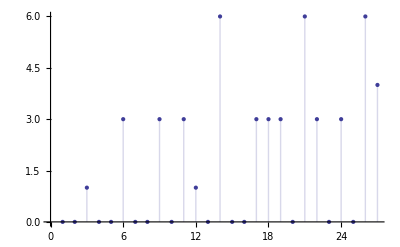

```mathematica
ListPlot[K,Filling->Axis]
```